```mathematica
p = ToExpression["(x_1 - 1)^2 + x_2^2 - 1/4", TeXForm]
```

-1/4+(-1+x_1)^2+x_2^2

```mathematica
f = {{ToExpression["-1/2x_1^3-x_1x_2^2+3/2x_1^2+x_2^2-11/8x_1+3/8", TeXForm]},
{ToExpression["-1/2x_2^3+1/8x_2", TeXForm]}}
```

{{3/8-(11 x_1)/8+(3 x_1^2)/2-x_1^3/2+x_2^2-x_1 x_2^2},{x_2/8-x_2^3/2}}

```mathematica
h = {{ToExpression["x_2", TeXForm]},{ToExpression["-x_1+1", TeXForm]}}
```

{{x_2},{1-x_1}}

```mathematica
y = 1/2 * Subscript[x, 1]*Subscript[x, 2]-1/2 Subscript[x, 2]
```

-x_2/2+(x_1 x_2)/2

```mathematica
f0 = f + h * y
```

{{3/8-(11 x_1)/8+(3 x_1^2)/2-x_1^3/2+x_2^2-x_1 x_2^2+x_2 (-x_2/2+(x_1 x_2)/2)},{x_2/8-x_2^3/2+(1-x_1) (-x_2/2+(x_1 x_2)/2)}}

```mathematica
f0 // TeXForm
```

\left(
\begin{array}{c}
 -\frac{x_1^3}{2}+\frac{3 x_1^2}{2}-x_2^2 x_1-\frac{11 x_1}{8}+x_2^2+x_2 \left(\frac{x_1
   x_2}{2}-\frac{x_2}{2}\right)+\frac{3}{8} \\
 -\frac{x_2^3}{2}+\frac{x_2}{8}+\left(1-x_1\right) \left(\frac{x_1 x_2}{2}-\frac{x_2}{2}\right) \\
\end{array}
\right)

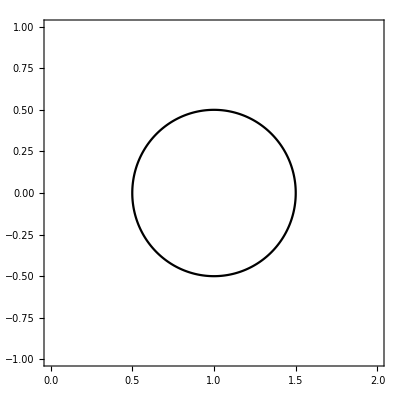

```mathematica
C1 = ContourPlot[p==0,{Subscript[x, 1],0,2},{Subscript[x, 2],-1,1},ContourStyle-> Black,PlotPoints->100,MaxRecursion->2]
```

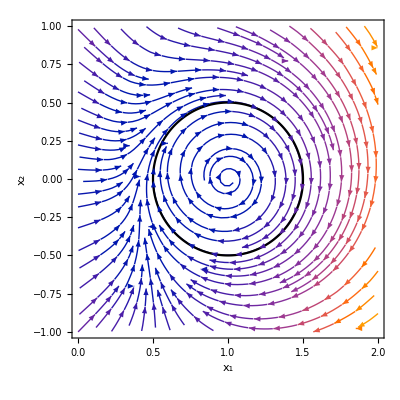

```mathematica
S1 = Show[StreamPlot[(f0 + h  * Subscript[x, 1]^2)[[;;, 1]],{Subscript[x, 1],0,2},{Subscript[x, 2],-1,1}], C1,FrameLabel-> {Subscript[x, 1],Subscript[x, 2]}]
```